# J/ψ Sub-threshold Production

## Initialization

```mathematica
Quit;
```

```mathematica
Clear["Global`*"];
Format[Mp,TraditionalForm]:=Style["M_p",FontColor->Blue];
Format[MJ,TraditionalForm]:=Style["M_(J/ψ)",FontColor->Blue];
```

```mathematica
val=<||>;
val["mass"]={Mp->0.9383,MJ->3.097};
```

## Models

```mathematica
ds2[s_,t_]:=Module[{x,v,R,F,W2,Ng},x=(2 Mp MJ + MJ^2)/(s-Mp^2);v=1/(16 π);R=1;Ng=7.567*10^3;F=Exp[1.13 t];(Ng v (1-x)^2/(R^2 MJ^2) F)/.val["mass"]];
```

```mathematica
ds23[s_,t_]:=Module[{x,v,R,F,W2,N2g,N3g},x=(2 Mp MJ + MJ^2)/(s-Mp^2);v=1/(16 π);R=1;N2g=6.499*10^3;N3g=2.894*10^3;F=Exp[1.13 t];(N2g v (1-x)^2/(R^2 MJ^2) F+N3g v 1/(R^4 MJ^4) F)/.val["mass"]];
```

```mathematica
tmin[s_]:=Module[{p,k,W,M1,M2},W=√s;p=((√((s-M1^2-M2^2)^2-4 M1^2 M2^2))/(2 W))/.{M1->0,M2->Mp};k=((√((s-M1^2-M2^2)^2-4 M1^2 M2^2))/(2 W))/.{M1->MJ,M2->Mp};(MJ^2-2 p √(MJ^2+k^2)-2 p k)/.val["mass"]];
tmax[s_]:=Module[{p,k,W,M1,M2},W=√s;p=((√((s-M1^2-M2^2)^2-4 M1^2 M2^2))/(2 W))/.{M1->0,M2->Mp};k=((√((s-M1^2-M2^2)^2-4 M1^2 M2^2))/(2 W))/.{M1->MJ,M2->Mp};(MJ^2-2 p √(MJ^2+k^2)+2 p k)/.val["mass"]];
```

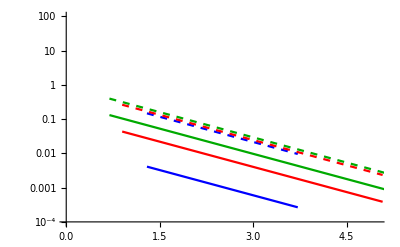

```mathematica
Show[LogPlot[{ds2[2*0.938*Eq+0.938^2,-t],ds23[16.82,-t]},{t,-tmax[16.82],-tmin[16.82]},PlotStyle->{{Blue},{Blue,Dashed}},PlotRange->{{0,5},{10^-4,10^2}}],LogPlot[{ds2[17.76,-t],ds23[17.76,-t]},{t,-tmax[17.76],-tmin[17.76]},PlotStyle->{{Red},{Red,Dashed}}],LogPlot[{ds2[18.70,-t],ds23[18.70,-t]},{t,-tmax[18.70],-tmin[18.70]},PlotStyle->{{Darker[Green]},{Darker[Green],Dashed}}]]
```

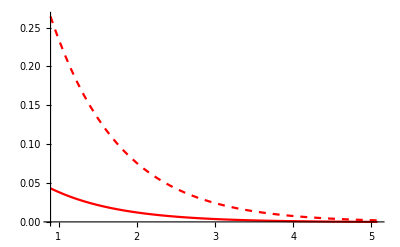

```mathematica
Plot[{ds2[17.76,-t],ds23[17.76,-t]},{t,-tmax[17.76],-tmin[17.76]},PlotStyle->{{Red},{Red,Dashed}},PlotRange->{Full,Full}]
```

```mathematica
ds23[17.76,-1]
```

0.235479

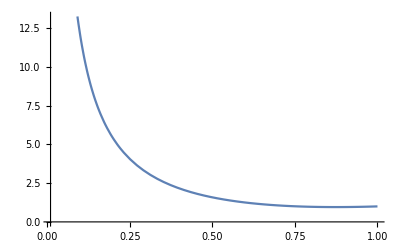

```mathematica
Plot[4/(3 y)-4/3+y^2,{y,0.01,1}]
```